### To do

Neutral case: Simulations of a sweep could use a very large population.  For the neutral case, I need to consider a smaller population - for example, 100 individuals for 1000 generations. This could be spliced onto a brief sweep.

Genealogies:  I need to store genomes in every generation, and then reconstruct genealogies along the genome.  The data needs to be savagely pruned, however.

SNP: Given the genealogies, throw down SNP onto the genomes.

Data formats: I need the current junctions scheme; tree-sequence; and Newick.

It is rather easy to identify branches, as ancestral to particular sets of genomes.  These have some persistence along the genome, and through time.

Reconstructing genealogies is non-trivial, but might be best done by identifying branches.  There could be an extremely large number of trivially different genealogies..

One can also throw down SNP relatively easily, just by setting a mutation rate.  This can also be done by branches, as long as one ensures that the set of all branches fills the whole ARG.

### Example: s=0.025, R=0.05, 2N=10^6, 100 genomes

In “”HH revisited” there was a single selected mutation that fixed. However, this sweep affects only a short region of genome: the rest is approximately neutral.  This example is of a hard sweep.

#### Iterating back

```mathematica
Dynamic[rep]
```

This sets up 10 replicate sweeps, with s=0.025, which take ~ 1000 generations:

```mathematica
mrx=makeRepsFix[0.025,10^6,10,1];
Dimensions/@mrx
```

{{1016},{922},{946},{959},{969},{870},{898},{885},{970},{1123}}

Using sweep #1 (1016 generations), this iterates 100 lineages back through time, to the beginning of the sweep. R=0.05, 2N=10^6.   This takes about 10 minutes; it slows down as the number .

```mathematica
Dynamic[{time,ng}]
```

```mathematica
pop0=Table[{1,{},{{i}}},{i,100}];time=0;
Timing[pl=FoldList[(time+=1;ng=Length[#1];iterC[#1,0.05,10^6,#2])&,pop0,Reverse[mrx⟦1⟧]];]
```

{1705.09,Null}

There are 3704 genomes ancestral to the sample. We delete all non-ancestral genomes, and then merge adjacent segments that define the same ancestry; this leaves 335 genomes that are relevant to coalescence within the sweep.

```mathematica
plf=deleteNC[pl⟦-1⟧];plfa=deleteNC[deleteAllNC[pl⟦-1⟧]];Length/@{pl⟦-1⟧,plf,plfa}
```

{3704,335,335}

Each genome is defined by the selected allele; the break-points; and the ancestry.  For example, this is a genome with the ancestral background, which has a region of  ~ 0.1cM ancestral to {12,84}:

```mathematica
plfa[[10]]
```

{0,{0.0472373,0.0481712},{{},{12,84},{}}}

There is a single copy of the favoured mutation, which is ancestral to the whole sample at the origin. As one goes further out, successive recombinations change the ancestry, though not exactly by one branch per event:

```mathematica
plfa[[-1]]
```

{1,{3.85122×10^-6,0.0000389163,0.0000529634,0.000092368,0.000177892,0.000185454,0.000240539,0.000252727,0.000256566,0.000279037,0.000291461,0.000306761,0.000307682,0.000315857,0.000316102,0.000330321,0.000361035,0.000376655,0.000384224,0.000397928,0.000481294,0.000507996,0.000514278,0.000570693,0.00058322,0.000631184,0.00068181,0.000714349,0.00074899,0.000762909,0.000799375,0.000841129,0.000846103,0.000878422,0.000886813,0.000898133,0.000975675,0.00108248,0.00108592,0.00110372,0.00112453,0.00128335,0.00132939,0.00138672,0.0014134,0.00143829,0.00144285,0.00154028,0.00155832,0.00156157,0.00162753,0.00163145,0.00165352,0.00166054,0.00168361,0.00169051,0.00171469,0.00171738,0.00176516,0.00178481,0.00179636,0.00182338,0.00182946,0.00184452,0.00185191,0.00185836,0.00187087,0.00187808,0.00191027,0.00195317,0.00195872,0.00196158,0.00207027,0.00208455,0.00215464,0.00215954,0.00218554,0.00221689,0.00224099,0.00224952,0.00229454,0.00236058,0.00236082,0.00240804,0.00241914,0.00242201,0.00242267,0.00246838,0.00263409,0.00265569,0.00267665,0.00273879,0.00281229,0.00283091,0.00286563,0.00297952,0.00306302,0.00316737,0.00318005,0.00319853,0.00320142,0.0032023,0.0032611,0.00330274,0.00331731,0.00336415,0.00344572,0.00355094,0.00355163,0.00356193,0.00356245,0.00357484,0.00364833,0.00365645,0.00368561,0.00370931,0.00372798,0.00374092,0.00374194,0.00380126,0.00388907,0.00390495,0.00398973,0.00404639,0.00406054,0.00408122,0.00408304,0.00410252,0.00420047,0.00431752,0.00431979,0.00440333,0.00445371,0.00447825,0.00451899,0.00455746,0.00463055,0.00464245,0.00471258,0.00472915,0.00480222,0.00480787,0.00486059,0.00494175,0.00496585,0.00496911,0.00497109,0.00500267,0.00504488,0.00512343,0.00512521,0.00517459,0.00522814,0.00527586,0.00542869,0.00546624,0.00546873,0.00554641,0.00563946,0.00570055,0.00573808,0.00585798,0.00600013,0.00605066,0.00611892,0.00613844,0.00614775,0.00619259,0.00624513,0.00630852,0.00631557,0.00643066,0.00658432,0.00658703,0.00670305,0.00691365,0.00703203,0.00708445,0.00736682,0.00784916,0.00807115,0.00873904,0.00886111,0.00919023,0.00921575,0.00926246,0.00929646,0.00932171,0.00980845,0.0101008,0.0101855,0.0104346,0.0105763,0.0117185,0.0150708,0.0164996},{{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,4,5,6,7,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,4,5,6,7,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,4,5,6,7,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,62,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,67,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,26,27,28,29,30,31,32,33,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,26,27,28,29,30,31,32,33,35,36,37,38,39,40,41,42,43,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,69,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,23,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,19,20,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,18,20,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,18,20,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,18,20,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,18,20,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,18,20,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,18,20,21,22,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,20,21,22,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,20,21,22,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,66,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,20,21,22,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,49,50,52,53,54,55,56,57,58,59,60,61,63,64,65,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,20,21,22,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,49,50,52,53,54,55,56,57,59,60,61,63,64,65,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,20,21,22,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,47,49,50,52,53,54,55,56,57,59,60,61,63,64,65,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,89,90,91,92,93,94,95,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,20,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,52,53,54,55,56,57,59,60,61,63,64,65,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,20,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,52,53,54,55,56,57,59,60,61,63,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,20,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,46,49,50,52,53,54,55,56,57,59,60,61,63,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99,100},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,20,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,46,49,50,52,53,54,55,56,57,59,60,61,63,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99},{1,2,3,5,6,7,9,10,11,12,13,15,16,17,20,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,52,53,54,55,56,57,59,60,61,63,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99},{1,2,3,5,6,7,9,10,11,12,15,16,17,20,24,27,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,52,53,54,55,56,57,59,60,61,63,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99},{1,2,3,5,6,7,9,10,11,12,15,16,17,20,24,27,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,52,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99},{1,2,3,5,6,7,9,10,11,12,15,16,17,20,24,27,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,52,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99},{2,3,5,6,7,9,10,11,12,15,16,17,20,24,27,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,52,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99},{2,3,5,6,7,9,10,11,12,15,16,17,20,24,27,29,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99},{2,3,5,6,7,9,10,11,12,15,16,17,20,24,27,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,90,91,92,93,94,95,97,98,99},{2,3,5,6,7,9,10,11,12,15,16,17,20,24,27,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,90,91,92,93,95,97,98,99},{2,3,5,6,7,9,10,11,12,15,16,17,20,22,24,27,30,31,32,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,90,91,92,93,95,97,98,99},{2,3,5,6,7,9,10,11,12,15,16,17,20,22,24,27,30,31,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,88,90,92,93,95,97,98,99},{2,3,5,6,7,9,10,11,12,15,16,17,20,22,24,27,30,31,33,34,35,36,37,38,39,40,41,43,44,45,46,49,50,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,90,92,93,95,97,98,99},{2,3,5,6,7,9,10,11,12,15,16,17,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,46,49,50,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,90,92,93,95,97,98,99},{2,3,6,7,9,10,11,12,15,16,17,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,46,49,50,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,83,84,85,86,87,90,92,93,95,97,98,99},{2,3,6,7,9,10,11,12,15,16,17,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,46,49,50,53,54,55,56,57,59,60,61,64,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,90,92,93,95,97,98,99},{2,3,6,7,9,10,11,12,15,16,17,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,46,49,50,53,54,55,56,57,59,60,61,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,90,92,93,95,97,98,99},{2,3,6,7,9,10,11,12,15,16,17,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,46,49,50,54,55,56,57,59,60,61,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,90,92,93,95,97,98,99},{2,3,6,7,9,10,11,12,15,16,17,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,46,49,50,54,55,57,59,60,61,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,90,92,93,95,97,98,99},{2,3,6,7,9,10,11,12,15,16,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,46,49,50,54,55,57,59,60,61,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,90,92,93,95,97,98,99},{2,3,6,7,9,10,11,12,15,16,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,60,61,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,90,92,93,95,97,98,99},{2,3,6,7,9,10,11,12,15,16,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,60,61,65,67,68,70,71,72,73,74,75,76,78,79,80,81,82,83,84,85,86,87,90,92,93,95,97,98,99,100},{2,3,6,7,9,10,11,12,15,16,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,60,61,65,67,68,70,71,72,73,74,75,76,79,80,81,82,83,84,85,86,87,90,92,93,95,97,98,99,100},{2,3,6,7,9,10,11,12,15,16,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,60,61,65,67,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,87,90,92,93,95,97,98,99,100},{2,3,6,7,9,10,11,12,15,16,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,60,61,65,67,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,87,90,92,93,95,97,99,100},{2,3,6,7,9,10,11,12,15,16,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,60,61,65,67,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,87,90,93,95,97,99,100},{2,3,6,7,9,10,11,12,15,16,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,60,61,65,67,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,87,90,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,16,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,61,65,67,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,87,90,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,16,20,22,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,61,65,67,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,90,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,16,20,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,61,65,67,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,20,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,61,65,67,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,20,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,61,65,67,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,20,24,27,30,31,33,34,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,61,65,67,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,20,24,27,30,31,33,34,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,65,68,70,71,72,73,74,75,79,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,20,24,27,30,31,33,34,35,36,37,38,39,40,41,43,44,45,49,50,54,55,57,59,65,68,70,71,72,73,74,75,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,20,24,27,30,31,33,34,35,36,37,38,39,40,41,43,44,45,49,50,54,57,59,65,68,70,71,72,73,74,75,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,20,24,27,30,31,33,34,35,36,37,38,39,40,41,43,44,45,49,50,54,57,59,65,66,68,70,71,72,73,74,75,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,20,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,57,59,65,66,68,70,71,72,73,74,75,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,20,24,27,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,57,59,65,66,68,70,72,73,74,75,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{2,3,6,7,9,10,11,12,15,20,24,27,28,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,57,59,65,66,68,70,72,73,74,75,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,3,6,7,9,10,11,12,15,20,24,27,28,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,57,59,65,66,68,70,72,73,74,75,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,3,6,7,9,10,11,12,15,20,24,27,28,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,57,59,65,66,70,72,73,74,75,80,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,3,6,7,9,10,11,12,15,20,24,27,28,30,31,33,35,36,37,38,39,40,41,43,44,45,49,50,54,57,59,65,66,70,72,73,74,75,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,3,6,7,9,10,11,12,15,20,24,27,28,30,31,33,35,36,37,38,39,40,41,43,44,45,50,54,57,59,65,66,70,72,73,74,75,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,3,6,7,9,10,11,12,15,20,24,27,28,30,31,33,35,36,38,39,40,41,43,44,45,50,54,57,59,65,66,70,72,73,74,75,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,3,6,7,9,10,11,12,15,20,24,26,27,28,30,31,33,35,36,38,39,40,41,43,44,45,50,54,57,59,65,66,70,72,73,74,75,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,3,6,7,9,10,11,12,15,20,24,26,27,28,30,31,33,35,36,38,39,40,41,43,44,45,50,54,57,59,60,65,66,70,72,73,74,75,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,6,7,9,10,11,12,15,20,24,26,27,28,30,31,33,35,36,38,39,40,41,43,44,45,50,54,57,59,60,65,66,70,72,73,74,75,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,7,9,10,11,12,15,20,24,26,27,28,30,31,33,35,36,38,39,40,41,43,44,45,50,54,57,59,60,65,66,70,72,73,74,75,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,9,10,11,12,15,20,24,26,27,28,30,31,33,35,36,38,39,40,41,43,44,45,50,54,57,59,60,65,66,70,72,73,74,75,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,9,10,11,12,15,20,24,26,27,28,30,31,33,35,36,38,39,40,41,43,44,45,50,54,57,59,60,65,66,70,72,73,74,75,78,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,9,10,11,12,15,20,24,26,27,28,30,31,33,35,36,38,39,40,41,43,44,45,50,54,57,60,65,66,70,72,73,74,75,78,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,9,10,11,12,15,20,24,26,27,28,30,31,33,35,38,39,40,41,43,44,45,50,54,57,60,65,66,70,72,74,75,78,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,9,10,11,12,15,20,24,26,27,28,30,31,35,38,39,40,41,43,44,45,50,54,57,60,65,66,70,72,74,75,78,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,9,10,11,12,15,20,24,26,27,28,30,31,35,38,39,40,41,43,44,50,54,57,60,65,66,70,72,74,75,78,81,82,83,84,85,86,88,93,95,96,97,99,100},{1,2,9,10,11,12,15,24,26,27,28,30,31,35,38,39,40,41,43,44,50,54,57,60,65,66,70,72,74,75,78,81,82,83,84,85,86,88,93,95,96,97,99,100},{2,9,10,11,12,15,24,26,27,30,35,38,39,40,43,44,50,54,60,65,66,70,72,74,75,78,81,82,83,84,86,88,93,96,97,100},{2,9,10,11,12,15,21,24,26,27,30,35,38,39,40,43,44,50,54,60,65,66,70,72,74,75,78,81,82,83,84,86,88,93,96,97,100},{2,9,10,11,12,15,21,24,26,27,30,35,38,39,40,43,44,50,52,54,60,65,66,70,72,74,75,78,81,82,83,84,86,88,93,96,97,100},{2,9,10,11,12,15,24,27,30,35,38,39,40,43,44,50,52,54,60,65,66,70,72,74,75,78,81,82,83,84,86,88,93,96,97,100},{2,9,10,11,12,15,24,27,30,35,38,39,40,43,44,50,52,54,60,65,66,70,72,74,75,78,81,82,83,84,86,88,93,96,97},{9,10,11,12,15,24,27,30,35,38,39,40,43,44,50,52,54,60,65,66,70,72,74,75,78,81,82,83,84,86,88,93,96,97},{9,10,11,12,15,22,24,27,30,35,38,39,40,43,44,50,52,54,60,65,66,70,72,74,75,78,81,82,83,84,86,88,93,96,97},{9,10,11,12,15,22,24,30,35,38,39,40,43,44,50,52,54,60,65,66,70,72,74,75,78,81,82,83,84,86,88,93,96,97},{9,10,11,12,15,22,24,30,35,38,39,40,43,44,52,54,60,65,66,70,72,74,75,78,81,82,83,84,86,88,93,96,97},{9,10,11,12,15,22,24,30,35,38,39,40,43,44,52,54,60,65,66,70,72,74,75,78,81,82,83,84,86,88,93,96},{9,10,11,12,15,22,24,30,35,38,39,40,43,44,52,54,60,65,66,70,74,75,78,81,82,83,84,86,88,93,96},{9,10,11,12,15,22,24,30,35,38,39,40,42,43,44,52,54,60,65,66,70,74,75,78,81,82,83,84,86,88,93,96},{9,10,11,12,15,22,24,30,35,38,39,40,42,43,44,52,54,60,65,66,70,74,75,78,81,82,83,84,86,93,96},{9,10,11,12,15,22,24,30,35,38,39,40,42,43,44,52,54,60,65,66,70,74,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,35,38,39,40,42,43,44,52,54,60,65,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,35,38,39,40,42,43,44,54,60,65,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,35,38,39,40,42,43,44,54,60,61,65,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,35,38,39,40,42,43,44,54,60,65,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,32,35,38,39,40,42,43,44,54,60,65,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,32,35,38,39,40,43,44,54,60,65,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,35,38,39,40,43,44,54,60,65,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,35,38,39,40,43,44,54,60,61,65,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,35,38,39,40,43,44,54,60,61,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,35,38,39,40,43,44,54,60,61,66,70,75,78,79,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,35,38,39,40,43,44,54,60,61,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,30,35,39,40,43,44,54,60,61,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,26,30,35,39,40,43,44,54,60,61,66,70,75,78,81,82,83,84,86,96},{9,10,11,12,15,22,24,26,30,35,39,40,43,44,54,60,61,66,75,78,81,82,83,84,86,96},{9,11,12,15,22,24,26,30,35,39,40,43,44,54,60,61,66,75,78,81,82,83,84,86,96},{9,11,12,15,22,24,26,30,31,35,39,40,43,44,54,60,61,66,75,78,81,82,83,84,86,96},{9,11,12,15,22,24,26,30,35,39,40,43,44,54,60,61,66,75,78,81,82,83,84,86,96},{9,11,12,15,22,24,26,30,35,39,40,43,44,54,60,61,66,69,75,78,81,82,83,84,86,96},{11,12,15,22,24,26,30,35,39,40,43,44,54,60,61,66,69,75,78,81,82,83,84,86,96},{11,12,22,24,26,30,35,39,40,43,44,54,60,61,66,69,75,78,81,82,83,84,86,96},{11,22,24,26,30,35,39,40,43,44,54,60,61,66,69,75,78,81,82,83,84,86,96},{11,22,24,26,30,35,39,40,43,44,54,60,61,66,69,75,76,78,81,82,83,84,86,96},{11,22,24,26,30,39,40,43,44,54,60,61,66,69,75,76,78,81,82,83,84,86,96},{11,22,24,26,30,39,40,43,44,54,60,61,69,75,76,78,81,82,83,84,86,96},{11,22,24,26,30,39,40,43,44,54,60,61,69,75,76,78,81,82,83,86,96},{11,22,24,26,30,39,40,43,44,54,60,61,67,69,75,76,78,81,82,83,86,96},{11,22,24,26,30,39,40,43,44,54,60,61,67,69,75,76,78,81,82,83,86,96,100},{11,22,24,26,29,30,39,40,43,44,54,60,61,67,69,75,76,78,81,82,83,86,96,100},{11,22,24,26,29,30,39,40,43,44,54,60,61,63,67,69,75,76,78,81,82,83,86,96,100},{11,22,24,26,29,30,39,40,43,44,54,60,61,63,67,69,75,76,78,81,82,83,96,100},{11,22,24,29,30,39,40,43,44,60,61,63,67,69,75,76,81,82,83,100},{11,22,24,29,30,39,40,43,44,60,61,63,69,75,76,81,82,83,100},{22,24,29,30,39,40,43,44,60,61,63,69,75,76,81,82,83,100},{24,29,30,39,40,43,44,60,61,63,69,75,76,81,82,83,100},{24,29,30,39,40,43,44,52,60,61,63,69,75,76,81,82,83,100},{24,29,30,39,40,43,44,52,60,61,63,69,76,81,82,83,100},{24,29,30,39,40,43,44,52,54,60,61,63,69,76,81,82,83,100},{24,29,30,39,40,43,44,46,52,54,60,61,63,69,76,81,82,83,100},{24,29,30,39,40,43,44,46,52,54,60,61,63,69,76,81,82,83,92,100},{24,29,30,39,40,43,44,46,52,54,61,63,69,76,81,82,83,92,100},{24,29,30,39,43,44,46,52,54,61,63,69,76,81,82,83,92,100},{24,29,30,39,43,44,46,52,54,61,63,69,76,80,81,82,83,92,100},{24,29,30,39,43,46,52,54,61,63,69,76,80,81,82,83,92,100},{24,29,30,39,43,46,52,54,59,61,63,69,76,80,81,82,83,92,100},{24,30,39,43,46,52,54,59,61,63,69,76,80,81,82,83,92,100},{24,30,39,43,46,52,54,59,61,63,69,76,80,81,82,83,92,96,100},{24,30,39,43,46,52,54,59,63,69,76,80,81,82,83,92,96,100},{12,24,30,39,43,46,52,54,59,63,69,76,80,81,82,83,92,96,100},{12,24,30,39,43,46,52,54,59,63,69,76,80,81,83,92,96,100},{12,24,30,43,46,52,54,59,63,69,76,80,81,83,92,96,100},{12,24,30,43,46,52,54,59,69,76,80,81,83,92,96,100},{12,30,43,46,52,54,59,69,76,80,81,83,92,96,100},{12,30,43,46,52,54,55,59,69,76,80,81,83,92,96,100},{12,30,43,52,54,55,59,69,76,80,81,83,92,96,100},{12,30,43,52,54,55,59,69,76,80,81,83,92,100},{12,30,43,52,54,55,59,69,76,80,81,83,92,93,100},{12,30,38,43,52,54,55,59,69,76,80,81,83,92,93,100},{12,22,30,38,43,52,54,55,59,69,76,80,81,83,92,93,100},{12,19,22,30,38,43,52,54,55,59,69,76,80,81,83,92,93,100},{12,19,22,30,38,43,52,54,55,59,76,80,81,83,92,93,100},{12,19,22,30,38,43,52,54,55,59,80,81,83,92,93,100},{12,19,22,30,38,52,54,55,59,80,81,83,92,93,100},{12,19,22,30,38,52,54,59,80,81,83,92,93,100},{12,19,22,30,38,52,54,59,69,80,81,83,92,93,100},{12,19,22,30,38,52,54,59,69,80,81,83,92,100},{12,19,22,30,38,52,54,59,69,80,83,92,100},{12,19,30,38,52,54,59,69,80,83,92,100},{12,19,30,38,52,54,59,62,69,80,83,92,100},{12,30,38,52,54,59,62,69,80,83,92,100},{12,38,52,54,59,62,69,80,83,92,100},{12,38,52,54,62,69,80,83,100},{12,38,52,54,62,69,83,100},{12,38,52,54,62,69,83,85,100},{38,52,54,62,69,83,85,100},{52,54,62,69,83,85,100},{5,52,54,62,69,83,85,100},{52,54,62,69,83,85,100},{52,54,69,83,85,100},{52,54,83,85},{52,83,85},{52,83,85,92},{52,83,85},{52,56,83,85},{16,52,56,83,85},{16,52,56,60,83,85},{2,16,52,56,60,83,85},{2,16,52,56,83,85},{2,16,52,83,85},{2,16,83,85},{16,83,85},{16,59,83,85},{16,59,83},{16,59},{},{52,56},{}}}

```mathematica
Length/@plfa[[-1,3]]
```

{100,99,98,97,96,95,96,95,94,92,91,90,89,90,89,87,88,87,86,85,84,83,82,83,82,83,82,81,82,77,78,77,76,77,75,74,75,74,73,72,71,72,70,68,67,66,67,66,65,64,63,62,63,62,61,60,59,60,59,58,56,55,56,57,55,54,53,54,53,52,53,54,53,52,51,50,51,52,51,50,49,50,49,47,46,45,44,36,37,38,36,35,34,35,34,33,32,31,32,31,30,29,28,29,28,29,28,27,28,27,28,27,26,27,26,25,26,25,26,25,24,23,24,23,22,21,22,23,24,25,24,20,19,18,17,18,17,18,19,20,19,18,19,18,19,18,19,18,19,18,17,16,15,16,15,14,15,16,17,18,17,16,15,14,15,14,13,12,13,12,11,9,8,9,8,7,8,7,6,4,3,4,3,4,5,6,7,6,5,4,3,4,3,2,0,2,0}

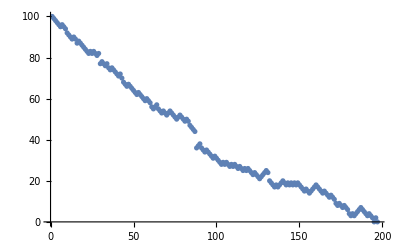

```mathematica
ListPlot[Length/@plfa[[-1,3]]]
```

These are the numbers of distinct ancestries along the genome.  Just a few genomes are ancestral to very many offspring - notably, the selected mutation.

```mathematica
Sort[Length/@plfa⟦All,3⟧]
```

{2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,6,7,7,7,7,7,7,7,7,8,11,14,17,40,197}

#### Looking at the ancestry carried by the initial genomes

```mathematica
tt=Table[TableForm[plfa⟦j⟧/.{{}->∅},TableDepth->2],{j,Length[plfa]}];
```

All but one of the initial 388 ancestral genomes are in background Q. These three contain small blocks:

```mathematica
tt⟦1;;10⟧
```

{0 |  | 
0.0374198 | 0.0379085 | 
∅ | {55,66} | ∅,0 |  |  |  | 
0.031793 | 0.0326039 | 0.0333491 | 0.0334629 | 
∅ | {7,49} | {7,31,49,57} | {7,49} | ∅,0 |  | 
0.00571403 | 0.00602181 | 
∅ | {41,75} | ∅,0 |  | 
0.00975611 | 0.0112833 | 
∅ | {17,23} | ∅,0 |  | 
0.0333491 | 0.0346484 | 
∅ | {31,57} | ∅,0 |  | 
0.0479868 | 0.0486157 | 
∅ | {57,69} | ∅,0 |  | 
0.0477957 | 0.0480043 | 
∅ | {12,67} | ∅,0 |  | 
0.0394593 | 0.0394885 | 
∅ | {1,56} | ∅,0 |  | 
0.00529687 | 0.00747562 | 
∅ | {45,94} | ∅,0 |  | 
0.0233161 | 0.0238922 | 
∅ | {23,79} | ∅}

The one special genome in background P contains coalescent material out to 0.6cM.

```mathematica
tt⟦-1⟧
```

1 |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
0.0000428966 | 0.000147038 | 0.000158428 | 0.000175816 | 0.00019124 | 0.000192531 | 0.00020494 | 0.000282017 | 0.00031625 | 0.000343128 | 0.0003444 | 0.000345808 | 0.000375238 | 0.000385571 | 0.000411007 | 0.000415426 | 0.000427574 | 0.000429708 | 0.000472651 | 0.000500404 | 0.000506952 | 0.000538607 | 0.000561573 | 0.000594298 | 0.000604979 | 0.000628679 | 0.000670651 | 0.000694636 | 0.00071236 | 0.000713397 | 0.000746807 | 0.000763962 | 0.000807149 | 0.000867774 | 0.000881101 | 0.000888377 | 0.000924061 | 0.000941551 | 0.000964125 | 0.000967561 | 0.00101264 | 0.00103345 | 0.001041 | 0.00104152 | 0.0010446 | 0.00109521 | 0.0011022 | 0.00112687 | 0.00114266 | 0.00115571 | 0.00117537 | 0.00119315 | 0.00121391 | 0.00125436 | 0.00131543 | 0.00134335 | 0.00139011 | 0.00143834 | 0.00144046 | 0.0014634 | 0.00148316 | 0.0014986 | 0.00154611 | 0.0016012 | 0.00160361 | 0.0016348 | 0.00163585 | 0.00166861 | 0.00170638 | 0.00175438 | 0.00175655 | 0.0017864 | 0.00181553 | 0.00181593 | 0.00191146 | 0.00196246 | 0.00200665 | 0.00201755 | 0.00202424 | 0.00210372 | 0.0021366 | 0.0021381 | 0.002145 | 0.0021498 | 0.00215304 | 0.00216613 | 0.00216791 | 0.00217324 | 0.00218107 | 0.00221465 | 0.00222561 | 0.00227863 | 0.0023431 | 0.00234457 | 0.00239171 | 0.0024024 | 0.00240835 | 0.0024752 | 0.00247876 | 0.00250004 | 0.00250542 | 0.00250995 | 0.00254491 | 0.00260113 | 0.00260912 | 0.0026285 | 0.00267101 | 0.00268166 | 0.00269263 | 0.00272936 | 0.00272938 | 0.00277366 | 0.00285349 | 0.0028782 | 0.00287979 | 0.00299088 | 0.00300531 | 0.00302197 | 0.00302309 | 0.00304252 | 0.00307186 | 0.00315196 | 0.00318713 | 0.00326579 | 0.00328173 | 0.00328875 | 0.00337003 | 0.00343601 | 0.00344649 | 0.00351382 | 0.00355031 | 0.00368805 | 0.00370039 | 0.00371387 | 0.00373513 | 0.00377256 | 0.0037769 | 0.00378858 | 0.00382976 | 0.00385127 | 0.00385327 | 0.00385767 | 0.00386645 | 0.00387859 | 0.00391999 | 0.00410818 | 0.00413001 | 0.00416474 | 0.00418825 | 0.00422609 | 0.00425756 | 0.00427729 | 0.00432313 | 0.0043623 | 0.00448931 | 0.00450853 | 0.00454322 | 0.00457355 | 0.00459037 | 0.00462107 | 0.00462258 | 0.00465758 | 0.00465993 | 0.00468764 | 0.00475888 | 0.0048018 | 0.00492198 | 0.00495543 | 0.00496884 | 0.00499464 | 0.00502381 | 0.00503625 | 0.0051221 | 0.00520283 | 0.00520942 | 0.00521131 | 0.00524854 | 0.0052824 | 0.00529687 | 0.00538207 | 0.00542557 | 0.00545754 | 0.00547053 | 0.00548583 | 0.00552678 | 0.00568813 | 0.00572113 | 0.00579569 | 0.00581692 | 0.00585402 | 0.00592816 | 0.00596373 | 0.00597746 | 0.00600309 | 
{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} | {1,2,3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100} | {1,2,3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,54,55,56,57,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,55,56,57,59,60,61,62,63,64,65,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,55,56,57,59,60,61,62,63,64,65,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,86,87,88,89,90,91,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,55,56,57,59,60,61,62,63,64,65,67,68,69,71,72,73,74,75,76,77,78,79,80,81,82,83,84,86,87,88,89,90,91,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,9,10,11,12,13,14,15,16,17,20,21,22,23,24,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,55,56,57,59,60,61,62,63,64,67,68,69,71,73,74,75,76,77,78,79,80,81,82,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,9,10,11,12,13,14,15,16,17,20,21,22,23,24,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,55,56,57,59,60,61,62,63,64,67,68,69,71,73,74,75,76,77,78,80,81,82,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,20,21,22,23,24,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,55,56,57,59,60,61,62,63,64,67,68,69,71,73,74,75,76,77,78,80,81,82,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,20,21,22,23,24,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,55,56,57,59,60,61,62,63,67,68,69,71,73,74,75,76,77,78,80,81,82,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,20,21,22,23,24,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,55,56,57,59,60,61,62,63,67,68,69,71,73,74,75,76,77,78,79,80,81,82,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,20,21,22,23,24,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,55,56,57,59,60,62,63,67,68,69,71,73,74,75,76,77,78,79,80,81,82,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,9,10,11,12,13,14,15,16,17,20,21,22,23,24,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,49,50,51,52,53,55,56,57,59,60,62,63,67,68,69,71,73,74,75,76,77,78,79,80,81,82,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,9,10,11,12,13,14,15,16,17,20,21,22,23,24,26,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,50,51,52,53,55,56,57,59,60,62,63,67,68,69,71,73,74,75,76,77,78,79,80,81,82,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,9,10,11,12,13,14,15,16,17,20,21,22,23,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,50,51,52,53,55,56,57,59,60,62,63,67,68,69,71,73,74,75,76,77,78,79,80,81,82,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,9,10,11,12,13,14,15,16,17,18,20,21,22,23,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,50,51,52,53,55,56,57,59,60,62,63,67,68,69,71,73,74,75,76,77,78,79,80,81,82,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,9,10,11,12,13,14,15,16,17,18,20,21,22,23,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,50,51,52,53,55,56,57,59,60,62,63,67,68,69,71,73,74,75,76,77,78,79,80,81,82,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,3,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,23,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,50,51,52,53,55,56,57,59,60,62,63,67,68,69,71,73,74,75,76,77,78,79,80,81,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,23,24,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,50,51,52,53,55,56,57,59,60,62,63,67,68,69,71,73,74,75,76,77,78,79,80,81,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,23,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,50,51,52,53,55,56,57,59,60,62,63,67,68,69,71,73,74,75,76,77,78,79,80,81,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,23,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,50,51,52,53,55,56,57,59,60,62,67,68,69,71,73,74,75,76,77,78,79,80,81,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,23,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,55,56,57,59,60,62,67,68,69,71,73,74,75,76,77,78,79,80,81,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,23,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,55,56,57,59,60,62,67,68,69,71,73,74,75,76,77,78,79,81,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,23,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,55,56,57,59,60,62,66,67,68,69,71,73,74,75,76,77,78,79,81,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,23,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,55,56,57,59,60,62,66,67,68,69,71,74,75,76,77,78,79,81,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,23,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,68,69,71,74,75,76,77,78,79,81,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,68,69,71,74,75,76,77,78,79,81,83,84,85,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,68,69,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,68,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,68,69,70,71,74,75,76,77,78,79,81,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,24,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,9,10,11,12,13,14,15,16,17,18,21,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,8,9,10,11,12,13,14,15,16,17,18,21,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,84,87,88,89,90,92,94,95,96,97,98,99,100} | {1,2,4,5,7,8,9,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,84,87,88,89,90,92,94,95,96,97,98,99,100} | {2,4,5,7,8,9,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,84,87,88,89,90,92,94,95,96,97,98,99,100} | {2,4,5,7,8,9,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {2,4,5,7,8,9,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,46,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {2,4,5,8,9,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,46,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {2,4,5,8,9,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {2,4,5,8,9,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {2,4,5,8,9,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {4,5,8,9,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {4,5,7,8,9,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {4,5,7,8,10,11,12,13,14,15,16,17,18,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {4,5,7,8,10,11,12,13,14,15,16,17,18,21,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {4,5,7,8,10,11,12,13,14,15,17,18,21,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,55,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {4,5,7,8,10,11,12,13,14,15,17,18,21,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99,100} | {4,5,7,8,10,11,12,13,14,15,17,18,21,22,24,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99} | {4,5,7,8,10,11,12,13,14,15,17,18,21,22,24,25,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,56,57,59,60,62,66,67,69,70,71,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99} | {4,5,7,8,10,11,12,13,14,15,17,18,21,22,24,25,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,56,57,59,60,62,66,67,69,70,71,72,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99} | {4,5,7,8,11,12,13,14,15,17,18,21,22,24,25,27,28,29,30,31,32,33,34,36,37,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,56,57,59,60,62,66,67,69,70,71,72,74,75,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99} | {4,5,7,8,11,12,13,14,15,17,18,21,22,24,25,27,28,29,30,31,32,33,34,36,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,56,57,59,60,62,66,67,69,70,71,72,74,76,77,78,79,81,83,84,87,88,89,90,92,94,95,96,97,98,99} | {4,5,7,8,11,12,13,14,15,17,18,21,22,24,25,27,28,29,30,31,32,34,36,38,39,40,41,42,43,44,45,47,48,49,51,52,53,54,56,57,59,60,62,66,67,69,70,71,72,74,76,77,78,79,81,83,87,88,89,90,92,94,95,96,97,98,99} | {5,7,8,11,12,14,15,17,18,21,22,24,25,27,28,34,36,38,43,44,47,48,49,51,52,53,54,56,59,60,62,66,67,69,71,72,74,76,78,79,81,83,88,89,90,92,94,96,97,99} | {5,7,8,11,12,14,15,17,18,19,21,22,24,25,27,28,34,36,38,43,44,47,48,49,51,52,53,54,56,59,60,62,66,67,69,71,72,74,76,78,79,81,83,88,89,90,92,94,96,97,99} | {5,7,8,11,12,14,15,17,18,19,21,22,24,25,27,28,34,36,38,43,44,47,48,49,51,52,53,54,56,59,60,62,66,67,69,71,72,74,76,78,79,81,88,89,90,92,94,96,97,99} | {5,7,8,11,12,14,15,17,18,19,21,22,24,25,27,34,36,38,43,44,47,48,49,51,52,53,54,56,59,60,62,66,67,69,71,74,76,78,79,81,88,89,90,92,94,96,97} | {5,7,8,11,12,14,15,17,18,19,21,22,24,25,27,34,36,38,43,44,47,48,49,51,52,53,54,56,59,60,62,66,67,69,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {5,7,8,11,14,15,17,18,19,21,22,24,25,27,34,36,38,43,44,47,48,49,51,52,53,54,56,59,60,62,66,67,69,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {5,7,8,11,14,15,17,18,19,21,22,24,25,27,34,36,38,43,44,47,48,49,51,52,53,54,56,59,62,66,67,69,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {5,7,8,11,14,15,17,18,19,21,22,24,25,27,34,36,43,44,47,48,49,51,52,53,54,56,59,62,66,67,69,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {2,5,7,8,11,14,15,17,18,19,21,22,24,25,27,34,36,43,44,47,48,49,51,52,53,54,56,59,62,66,67,69,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {2,5,7,8,11,14,15,17,18,19,21,22,24,25,27,34,36,43,44,47,48,49,51,52,53,54,56,59,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {2,5,7,8,11,14,15,17,18,19,21,22,24,25,27,34,36,38,43,44,47,48,49,51,52,53,54,56,59,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {2,5,7,8,11,14,15,17,18,19,21,22,24,27,34,36,38,43,44,47,48,49,51,52,53,54,56,59,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {2,5,7,8,11,14,15,17,18,19,21,22,24,27,36,38,43,44,47,48,49,51,52,53,54,56,59,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {2,5,7,8,11,14,15,17,18,19,21,22,24,27,36,38,43,44,47,49,51,52,53,54,56,59,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {2,3,5,7,8,11,14,15,17,18,19,21,22,24,27,36,38,43,44,47,49,51,52,53,54,56,59,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {2,3,5,7,8,11,14,15,17,18,19,21,22,24,27,36,38,43,44,47,49,51,52,53,54,56,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94,96,97} | {2,3,5,7,8,11,14,15,17,18,19,21,22,24,27,36,38,43,44,47,49,51,52,53,54,56,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94,96} | {2,3,5,7,8,11,14,15,17,18,19,21,22,24,27,36,38,43,44,47,48,49,51,52,53,54,56,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94,96} | {2,3,5,7,8,11,14,15,17,18,19,21,22,24,27,36,38,43,44,47,48,49,52,53,54,56,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94,96} | {2,3,5,7,8,11,14,15,17,18,19,21,22,24,27,36,38,43,44,47,48,49,52,53,54,56,62,66,67,71,74,76,78,79,81,88,89,90,91,92,94} | {2,3,5,7,8,11,14,15,17,18,19,21,22,24,27,36,38,43,44,47,48,49,52,53,54,56,62,66,67,71,74,76,78,79,81,88,89,90,91,94} | {2,3,5,7,8,11,14,15,17,18,19,21,22,24,27,36,38,43,44,47,48,49,52,53,54,56,62,66,67,71,72,74,76,78,79,81,88,89,90,91,94} | {2,3,5,7,8,11,14,15,19,21,22,24,27,36,38,43,44,47,48,49,52,53,54,56,62,66,67,71,72,74,76,78,79,81,88,89,90,94} | {2,3,5,7,8,11,14,15,19,21,22,24,27,36,38,43,44,47,48,49,52,53,54,62,66,67,71,72,74,76,78,79,81,88,89,90,94} | {2,3,5,7,8,11,14,15,19,21,22,24,27,36,38,42,43,44,47,48,49,52,53,54,62,66,67,71,72,74,76,78,79,81,88,89,90,94} | {2,3,5,7,8,11,14,15,19,21,22,24,27,36,38,42,43,44,47,48,49,52,53,54,56,62,66,67,71,72,74,76,78,79,81,88,89,90,94} | {2,3,5,7,8,11,14,15,19,21,22,24,27,36,38,42,43,44,48,49,52,53,54,56,62,66,67,71,72,74,76,78,79,81,88,89,90,94} | {2,3,5,7,8,11,14,15,19,21,22,24,27,32,36,38,42,43,44,48,49,52,53,54,56,62,66,67,71,72,74,76,78,79,81,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,24,27,32,36,38,42,43,44,48,49,52,53,54,56,62,66,67,71,72,74,76,78,79,81,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,24,27,32,36,38,42,43,44,48,49,52,53,54,56,62,66,67,71,72,74,76,77,78,79,81,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,24,27,36,38,42,43,44,48,49,52,53,54,56,62,66,67,71,72,74,76,77,78,79,81,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,24,27,28,36,38,42,43,44,48,49,52,53,54,56,62,66,67,71,72,74,76,77,78,79,81,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,24,27,28,36,38,42,44,48,49,52,53,54,56,62,66,67,71,72,74,76,77,78,79,81,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,24,27,28,34,36,38,42,44,48,49,52,53,54,56,62,66,67,71,72,74,76,77,78,79,81,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,27,28,34,36,38,42,44,48,49,52,53,54,56,62,66,67,71,72,74,76,77,78,79,81,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,27,28,34,36,38,42,44,48,49,52,53,54,56,62,66,67,71,72,74,76,77,78,79,81,85,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,27,28,34,36,38,42,44,48,49,52,53,54,56,62,67,71,72,74,76,77,78,79,81,85,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,27,28,34,36,38,42,44,48,49,52,53,54,62,67,71,72,74,76,77,78,79,81,85,88,89,90,94} | {2,3,5,8,11,14,15,19,21,22,27,28,34,36,38,42,44,48,49,52,53,54,62,64,67,71,72,74,76,77,78,79,81,85,88,89,90,94} | {3,5,8,11,14,15,19,21,22,27,28,34,36,38,42,44,48,49,52,53,54,62,64,67,71,72,74,76,77,78,79,81,85,88,89,90,94} | {3,5,8,11,14,15,19,21,22,27,28,34,35,36,38,42,44,48,49,52,53,54,62,64,67,71,72,74,76,77,78,79,81,85,88,89,90,94} | {3,5,8,11,14,19,21,22,27,28,34,35,36,38,42,44,48,49,52,53,54,62,64,67,71,72,74,76,77,78,79,81,85,88,89,90,94} | {3,5,8,11,14,19,21,22,27,28,34,35,36,38,42,44,48,49,52,54,62,64,67,71,72,74,76,77,78,79,81,85,88,89,90,94} | {3,5,8,11,14,19,21,22,27,28,34,35,36,38,42,44,48,49,52,54,62,64,67,71,72,74,76,77,78,79,81,85,88,90,94} | {3,5,8,11,14,19,21,22,27,28,34,35,36,38,42,44,48,49,52,54,56,62,64,67,71,72,74,76,77,78,79,81,85,88,90,94} | {3,5,8,11,14,19,21,22,27,28,34,35,36,38,42,44,48,49,52,53,54,56,62,64,67,71,72,74,76,77,78,79,81,85,88,90,94} | {3,5,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,53,54,56,62,64,67,71,72,74,76,77,78,79,81,85,88,90,94} | {3,5,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,53,54,56,62,64,65,67,71,72,74,76,77,78,79,81,85,88,90,94} | {3,5,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,53,54,56,62,64,65,67,71,72,74,76,78,79,81,85,88,90,94} | {3,5,6,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,53,54,56,62,64,65,67,71,72,74,76,78,79,81,85,88,90,94} | {5,6,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,53,54,56,62,64,65,67,71,72,74,76,78,79,81,85,88,90,94} | {5,6,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,53,54,56,64,65,67,71,72,74,76,78,79,81,85,88,90,94} | {5,6,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,53,54,56,64,65,67,72,74,76,78,79,81,85,88,90,94} | {5,6,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,53,54,55,56,64,65,67,72,74,76,78,79,81,85,88,90,94} | {5,6,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,53,54,55,64,65,67,72,74,76,78,79,81,85,88,90,94} | {5,6,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,53,54,55,61,64,65,67,72,74,76,78,79,81,85,88,90,94} | {5,6,8,11,14,19,21,22,28,34,35,36,38,42,44,48,49,52,54,55,61,64,65,67,72,74,76,78,79,81,85,88,90,94} | {5,6,8,11,14,19,21,22,28,34,35,36,38,39,42,44,48,49,52,54,55,61,64,65,67,72,74,76,78,79,81,85,88,90,94} | {5,6,8,11,14,19,21,22,28,34,35,36,38,39,42,44,48,49,52,55,61,64,65,67,72,74,76,78,79,81,85,88,90,94} | {5,8,11,14,19,21,22,28,34,35,36,38,39,42,44,48,49,52,55,61,64,65,67,72,74,76,78,79,81,85,88,90,94} | {5,8,11,14,19,21,22,34,35,36,38,39,42,44,48,49,52,55,61,64,65,67,72,74,76,78,79,81,85,88,90,94} | {5,8,11,14,19,21,22,34,35,36,38,39,42,44,48,49,52,55,61,64,65,67,72,74,76,78,79,80,81,85,88,90,94} | {5,8,11,14,19,21,22,34,35,36,38,42,44,48,49,52,55,61,64,65,67,72,74,76,78,79,80,81,85,88,90,94} | {5,8,14,19,21,22,34,35,36,38,42,44,48,49,52,55,61,64,65,67,72,74,76,78,79,80,81,85,88,90} | {5,8,14,19,21,22,34,35,36,38,42,44,48,49,52,55,61,62,64,65,67,72,74,76,78,79,80,81,85,88,90} | {5,8,14,19,21,22,34,35,36,38,42,44,48,49,52,55,61,62,64,65,67,72,74,76,78,79,80,81,85,90} | {5,8,14,19,21,22,35,36,38,42,44,48,49,52,55,61,62,64,65,67,72,74,76,78,79,80,81,85,90} | {5,8,14,19,21,22,35,36,38,42,44,48,49,52,55,61,62,64,65,67,72,74,76,78,79,80,81,82,85,90} | {5,8,14,19,21,22,35,36,38,42,44,46,48,49,52,55,61,62,64,65,67,72,74,76,78,79,80,81,82,85,90} | {5,8,14,19,21,22,35,36,38,42,44,46,48,49,52,55,62,64,65,67,72,74,76,78,79,80,81,82,85,90} | {5,8,14,19,21,22,35,36,38,42,44,46,48,49,52,55,62,64,65,67,72,76,78,79,80,81,82,85,90} | {5,8,14,19,21,35,36,38,42,44,46,48,49,52,55,62,64,65,67,72,76,78,79,80,81,82,85,90} | {5,8,14,19,21,35,36,38,42,44,46,48,49,52,55,62,64,65,67,76,78,79,80,81,82,85,90} | {5,8,14,19,21,35,36,38,42,44,46,48,49,52,55,62,64,65,67,78,79,80,81,82,85,90} | {5,8,14,19,21,35,36,38,42,44,46,49,52,55,62,64,65,67,78,79,80,81,82,85,90} | {5,8,14,19,21,35,38,42,44,46,49,52,55,62,64,65,67,78,79,80,81,82,85,90} | {5,8,14,19,21,35,38,42,44,46,49,52,55,62,64,65,66,67,78,79,80,81,82,85,90} | {5,8,14,19,21,35,38,42,44,46,49,52,55,62,64,65,66,78,79,80,81,82,85,90} | {5,8,14,19,21,35,38,42,44,46,49,52,55,62,64,65,66,78,79,80,81,82,85,89,90} | {5,8,9,14,19,21,35,38,42,44,46,49,52,55,62,64,65,66,78,79,80,81,82,85,89,90} | {5,8,9,14,19,21,35,38,42,44,46,49,52,55,62,65,66,78,79,80,81,82,85,89,90} | {5,8,9,14,19,21,35,38,42,44,46,49,52,55,62,65,66,78,79,80,81,82,85,89,90,92} | {5,7,8,9,14,19,21,35,38,42,44,46,49,52,55,62,65,66,78,79,80,81,82,85,89,90,92} | {5,7,8,9,14,19,21,35,38,42,44,46,49,52,55,62,65,78,79,80,81,82,85,89,90,92} | {5,7,8,9,19,21,35,38,42,44,46,49,52,55,62,65,78,79,80,81,82,85,89,90,92} | {7,8,9,19,21,35,38,44,46,49,52,55,62,65,78,79,80,81,82,85,89,90,92} | {7,8,9,19,21,35,38,44,46,49,52,55,62,65,78,79,80,81,82,85,90,92} | {7,8,9,19,21,35,38,44,46,49,52,55,62,65,74,78,79,80,81,82,85,90,92} | {7,8,9,19,35,38,44,46,49,52,55,62,65,74,78,79,80,81,82,85,90,92} | {7,8,9,19,35,38,44,46,49,52,55,62,63,65,74,78,79,80,81,82,85,90,92} | {7,8,9,19,29,35,38,44,46,49,52,55,62,63,65,74,78,79,80,81,82,85,90,92} | {7,8,9,19,29,35,38,44,46,49,52,55,62,63,65,74,78,79,80,81,82,85,90,92,96} | {7,8,9,19,29,35,38,42,44,46,49,52,55,62,63,65,74,78,79,80,81,82,85,90,92,96} | {7,8,9,19,29,35,38,42,44,46,49,52,55,62,63,65,74,78,79,80,81,82,85,90,92,94,96} | {7,8,9,19,29,35,38,42,44,46,49,52,55,62,63,65,78,79,80,81,82,85,90,92,94,96} | {7,8,9,29,35,38,42,44,46,49,52,55,62,63,65,78,79,80,81,82,85,90,92,94,96} | {7,8,9,29,35,38,42,46,49,52,55,62,63,65,78,79,80,81,82,85,90,92,94,96} | {8,9,29,35,38,42,46,49,52,55,62,63,65,78,79,80,81,82,85,90,92,94,96} | {1,8,9,29,35,38,42,46,49,52,55,62,63,65,78,79,80,81,82,85,90,92,94,96} | {1,8,9,29,35,38,42,46,49,52,55,62,63,65,78,79,81,82,85,90,92,94,96} | {1,8,9,29,35,38,42,46,49,52,55,62,63,65,78,79,81,82,83,85,90,92,94,96} | {1,8,9,29,35,38,42,46,49,52,55,62,63,65,78,81,82,83,85,90,92,94,96} | {1,8,9,29,35,37,38,42,46,49,52,55,62,63,65,78,81,82,83,85,90,92,94,96} | {1,9,29,35,37,38,42,46,49,52,55,62,63,65,78,81,82,83,85,90,92,94,96} | {1,9,29,35,37,38,42,46,49,52,55,56,62,63,65,78,81,82,83,85,90,92,94,96} | {1,9,29,35,37,38,42,46,49,52,55,56,62,63,65,67,78,81,82,83,85,90,92,94,96} | {1,9,29,35,37,38,42,46,49,52,55,56,63,65,67,78,81,82,83,85,90,92,94,96} | {1,9,29,35,37,38,42,46,49,52,55,56,63,65,78,81,82,83,85,90,92,94,96} | {1,9,29,35,37,38,42,46,49,52,55,56,63,65,72,78,81,82,83,85,90,92,94,96} | {1,9,29,35,37,38,42,46,49,52,55,56,63,65,72,73,78,81,82,83,85,90,92,94,96} | {1,9,29,35,37,38,42,46,52,55,56,63,65,72,73,78,81,82,83,85,90,92,94,96} | {1,9,29,35,37,38,42,46,52,55,56,63,65,72,73,78,81,82,85,90,92,94,96} | {1,9,29,35,37,38,42,46,52,55,56,63,65,72,73,76,78,81,82,85,90,92,94,96} | {1,9,22,29,35,37,38,42,46,52,55,56,63,65,72,73,76,78,81,82,85,90,92,94,96} | {1,9,22,29,35,37,42,46,52,55,56,63,65,72,73,76,78,81,82,85,90,92,94,96} | {1,9,22,29,35,37,42,46,52,55,56,63,65,72,73,76,78,81,82,85,89,90,92,94,96} | {1,9,22,29,35,37,42,46,52,55,56,63,65,72,73,76,78,81,82,85,89,90,91,92,94,96} | {1,9,22,29,35,37,42,46,52,55,56,63,65,72,73,76,78,82,85,89,90,91,92,94,96} | {1,9,22,29,35,37,42,46,52,55,56,63,65,72,73,76,78,82,85,89,90,92,94,96} | {1,9,22,29,35,37,42,46,52,55,56,63,65,72,73,76,78,82,85,89,90,94,96} | {1,9,22,29,35,37,42,46,52,55,56,63,65,72,73,76,78,82,85,89,94,96} | {1,9,22,29,35,37,42,46,52,55,56,63,65,72,73,76,78,82,85,89,94} | {1,9,22,29,35,37,42,46,52,55,56,63,65,72,73,76,78,82,85,89} | {1,9,22,29,35,37,42,46,52,55,56,65,72,73,76,78,82,85,89} | {1,9,22,29,35,37,46,52,55,56,65,72,73,76,78,82,85,89} | {1,9,22,29,35,37,43,46,51,52,55,56,65,72,73,76,78,82,85,89} | {1,9,22,29,35,37,43,46,51,52,55,65,72,73,76,78,82,85,89} | {1,9,22,29,35,37,43,46,51,52,55,65,72,73,76,78,82,85,89,98} | {1,9,22,29,35,37,43,46,51,52,55,65,72,73,76,78,82,89,98} | {1,9,22,29,35,37,43,46,51,52,55,65,72,73,76,78,82,89} | {1,9,11,22,29,35,37,43,46,51,52,55,65,72,73,76,78,82,89} | {9,11,22,29,35,37,43,46,51,52,55,65,72,73,76,78,82,89} | {9,11,22,35,37,43,46,51,52,55,65,72,73,76,78,82,89} | {9,11,22,35,37,43,46,51,52,55,72,73,76,78,82,89} | {1,9,11,22,35,37,43,46,51,52,55,72,73,76,78,82,89} | {1,9,11,22,35,37,43,46,51,52,55,72,73,76,78,89} | {1,9,11,22,35,37,46,51,52,55,72,73,76,78,89} | ∅

#### Plotting ancestry of the 100 genomes

There is expected to be a lot of coalescence across the whole region:

```mathematica
1018 10^-6(100 99/2.)
```

5.0391

```mathematica
Log[10^6 0.025]/0.025
```

405.065

The region with complete coalescence is in this case quite small, and not entirely due to original mutation:

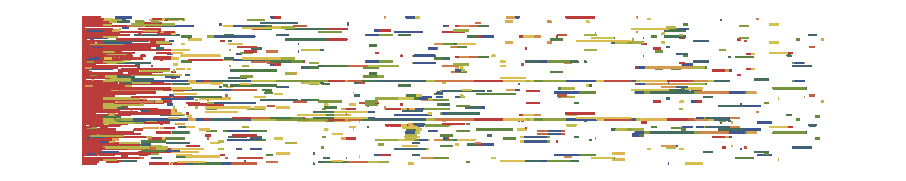

```mathematica
cf=ColorData["DarkRainbow"];
Graphics[plotAncestry[100,plfa,cf],AspectRatio->0.2]
```

This plots out to 1cM:

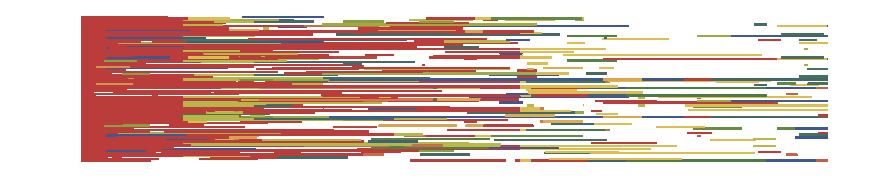

```mathematica
cf=ColorData["DarkRainbow"];
Graphics[plotAncestry[100,plfa,cf],AspectRatio->0.2,PlotRange->{{0,0.01},{-0.5,100.5}}]
```

#### Examining the data structures

### Neutral case

#### Iterating back for 10×2N generations; n=2N=100; R=0.05

This iterates 100 lineages back through time; R=0.05, 2N=100.

```mathematica
Dynamic[{time,ng}]
```

```mathematica
n=100;
pop0=Table[{0,{},{{i}}},{i,n}];time=0;
Timing[pl=NestList[(time+=1;ng=Length[#1];iterC[#1,0.05,n])&,pop0,10n];]
```

{1.41707,Null}

We now merge adjacent blocks with the same ancestry, and delete non-ancestral genomes.  This reduces the # early on, but not later.  In the later stages, 2-10 genomes carry the ancestry - but all genealogies have coalesced.

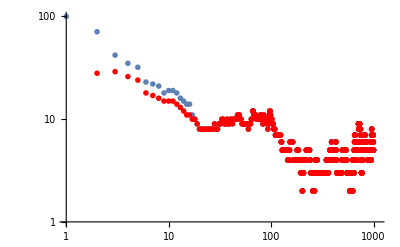

```mathematica
pla=deleteNC[deleteAllNC[#]]&/@pl;
Show[ListLogLogPlot[Length/@pl,PlotRange->{{1,1100},{1,100}},PlotStyle->PointSize[0.01]],ListLogLogPlot[Length/@pla,PlotStyle->{PointSize[0.01],Red}]]
```

```mathematica
Dynamic[{time,ng}]
```

#### Iterating back until coalescence; n=2N=100; R=0.1

This is very fast. It takes 478 generations until complete coalescence:

```mathematica
Dynamic[{time,nGenes}]
```

```mathematica
Timing[time=0;pl2=makeC[100,0.1,100];Length[pl2]]
```

{1.65355,478}

The # of ancestral lineages drops rapidly at first, but then stabilises around 2 N_e r=10.

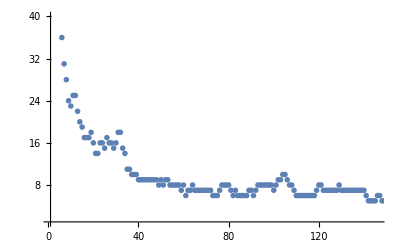

```mathematica
ListPlot[Length/@pl2,PlotRange->{{1,146},{1,40}},PlotStyle->PointSize[0.01]]
```

#### Identifying branches

Here, each instance is a lineage and a generation.  The extent of a branch along the genome and through time may be complex. The numbers of times each branch appears is highly skewed. Two branches appear >1000 times, but there are 85 instances once, and the median is 7.

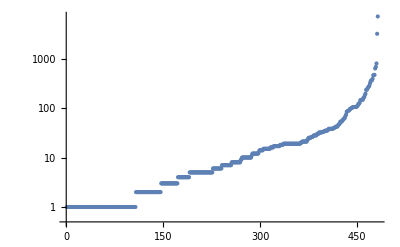

{478.,482.,25439.,7.,52.778}

```mathematica
tb=branchList[pl2];
ListLogPlot[Sort[Last/@tb],PlotRange->All]
{Length[pl2],Length[tb],Total[Last/@tb],Median[Last/@tb],Mean[Last/@tb]}//N
```

This plots 478 generations on the vertical axis, and ma length R=0.1 on the horizontal.   of the 482 blocks is coloured in according to the number of instances  (red is high)(approximately the # of generations).  However, many are overlaid in this representation.

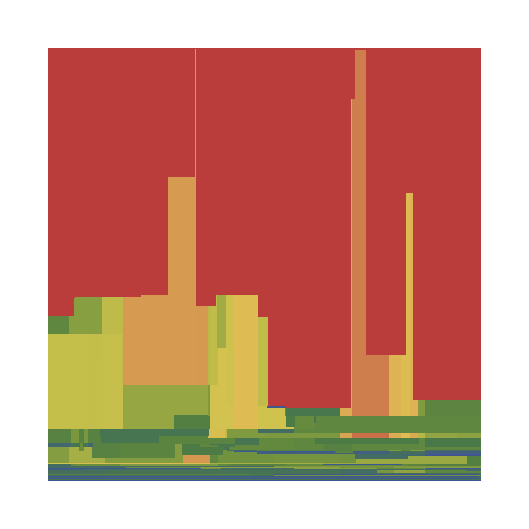

```mathematica
tb=branchList[pl2];
mx=Max[Log[Last/@tb]];cf=ColorData["DarkRainbow"];
Show[plotBranch[#⟦1⟧,cf[Log[#⟦2⟧]/mx],pl2,0.1]&/@tb,PlotRange->{{0,0.1},{0,478}},AspectRatio->1]
```

This shows three sets of 1 in 10 lineages. Again, colour corresponds to timespan. Note the inverse relation between block length and timespan:

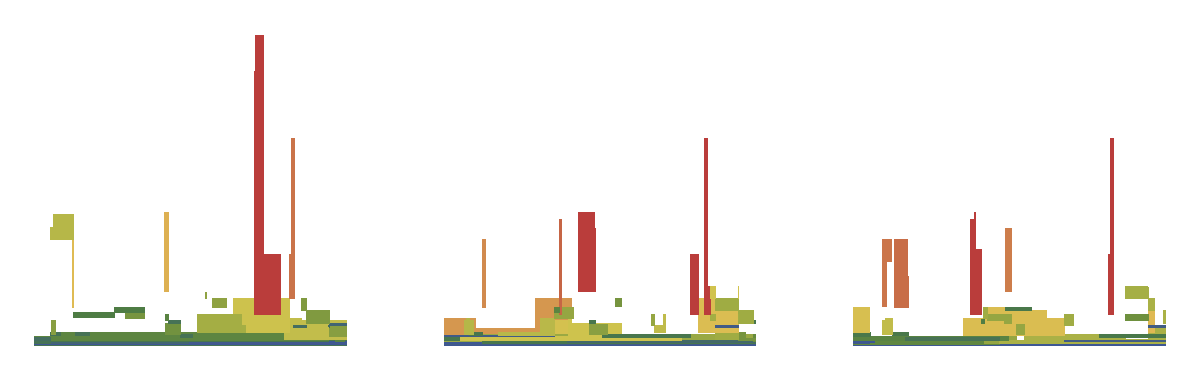

```mathematica
tbs[j_,k_]:=branchList[pl2]⟦j;;-1;;k⟧;cf=ColorData["DarkRainbow"];
gr[j_,k_]:=Module[{mx=Max[Log[Last/@tbs[j,k]]]},
Show[plotBranch[#⟦1⟧,cf[Log[#⟦2⟧]/mx],pl2,0.1]&/@tbs[j,k],PlotRange->{{0,0.1},{0,478}},AspectRatio->1]];
GraphicsRow[gr[#,10]&/@{1,2,3}]
```

#### inverse relation between block length and timespan

This shows the mean block length against its timespan.  The 482 branches are shown by blue dots, and the mean for each timespan is shown by the red dots.  There is an inverse relation, but as ~ t^-0.6, rather than the expected t^-1.   The two fits are to the blue vs the red dots; the black line is 0.3 t^-1, to indicate the slope expected with a simple inverse relation.

```mathematica
txl=(pb=posBlock[pl2,#⟦1⟧,0.1];
{Length[Union[pb⟦All,1⟧]],Mean[pb⟦All,2⟧.{-1,1}]})&/@tb;
txlm=Mean/@GatherBy[txl,Log[#⟦1⟧]&];
```

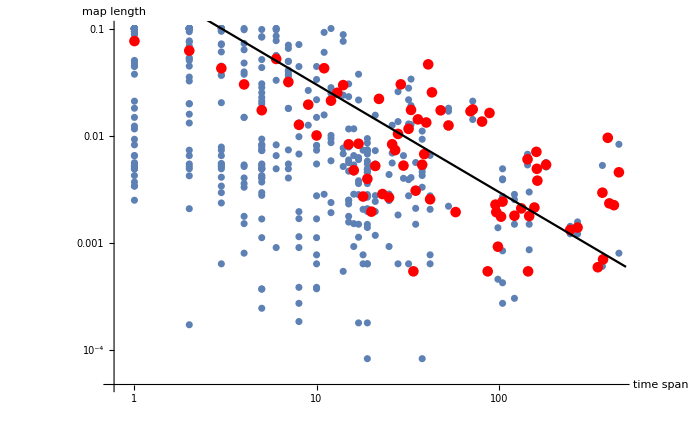

{-3.1815-0.657731 t,-2.76384-0.609253 t}

```mathematica
Show[ListLogLogPlot[txl],ListLogLogPlot[txlm,PlotStyle->Red],LogLogPlot[0.3 t^-1,{t,1,500},PlotStyle->Black],
AxesLabel->{"time\nspan","map\nlength"}]
{Fit[Log[txl],{1,t},t],Fit[Log[txlm],{1,t},t]}
```

This shows timespan plotted against map length - it is not obvious which direction causality runs. Now, we fit a relation t~r^-0.7 which contradicts the above fit, r~t^-0.6. Maybe, a direct inverse relation t~r^-1 is possible ?  The black line is 0.4 r^-1, to indicate the slope expected with a simple inverse relation

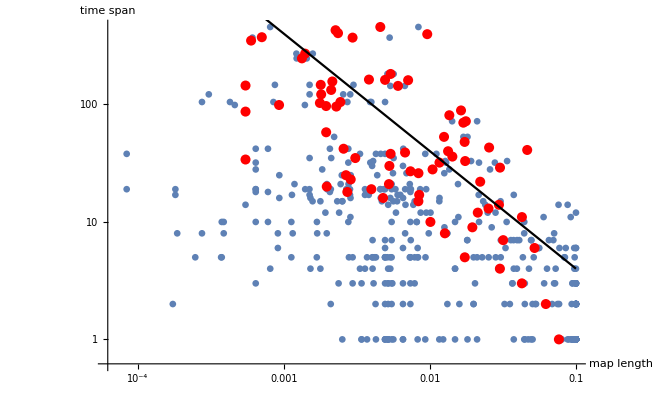

{-0.475329-0.547026 r,0.138248-0.717338 r}

```mathematica
Show[ListLogLogPlot[Reverse/@txl],ListLogLogPlot[Reverse/@txlm,PlotStyle->Red],LogLogPlot[0.4 x^-1,{x,10^-4,0.1},PlotStyle->Black],AxesLabel->{"map\nlength","time\nspan"}]
{Fit[Log[Reverse/@txl],{1,r},r],Fit[Log[Reverse/@txlm],{1,r},r]}
```

#### email to Miso

Dear Miso & Dasha,

I’m puzzling over the distribution of haplotype block lengths and timespans, and I think am just being confused by elementary regression. Maybe you can help.

I simulate the neutral coalescent with recombination, following a map length R-0.1 (10cM), through a population of 100 genomes, and start by sampling all of them. Tracing back, I identify “branches” that are ancestral to particular sets of genes.  Tracing back through time, these arise when coalescence brings together some set of lineages, and end through further coalesce events. Tracing along the genome, they end when recombination changes the genealogy.  Thus. one expects the span along the genome to be shorter for branches with a longer timespan, because these suffer a higher rate of recombination.  One can see this in the picture below, which shows three random subsets of blocks (the genome runs horizontally, time vertically).  There are tall thin blocks (i.e., which last a long time but only within a shrt map distance) and wide shallow blocks (including the tips of the genealogy).

For each branch, I can plot the timespan and its extent along the genome (blue dots below); I can also aggregate all branches with the same timespan, and take their mean map length (red dots).  If I regress map length on timespan, I get r~t^-0.66, but if I regress map length on timespan, I get t~r^-0.55 (roughly) which is a contradiction - and both differ from t^r^-1.  I guess this is just because I am fitting different models (which variable is a function of which?) - but it’s not clear what the “right” model is.

We are just writing a “conceptual” paper on how to define haplotypes, so working out the theory in full isn’t essential - but I’d like to understand!

Best regards,

Nick

#### Throwing down SNP

Each block represents a target for mutations puts them onto the genomes; one can also record the ages of the SNP. For every instance, one draws SNP randomly, and then assigns them to a time and map position.  Given a list of SNP, grouped by branch, one then assembles the genomes.

This generates a list of SNP for each of the 481 branches. The distribution of # SNP per branch (on a log_10 scale) is very broad:

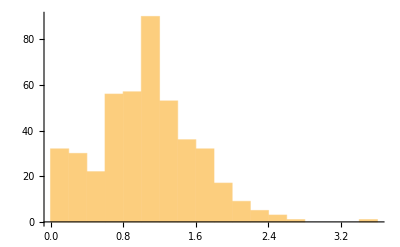

13410

```mathematica
tb=branchList[pl2];
snp=makeSNP[posBlock[pl2,#⟦1⟧,0.1],100]&/@tb;
Histogram[Log[10,Length/@snp],PlotRange->All]
Total[Length/@snp]
```

#### addSNP

```mathematica
addSNP::usage="addSNP[{{b_1,k_1},…},{{{t_(1, 1),x_(1, 1)},…},…}] generates an array genomes×SNP, in the form {{t_1,x_1,k_1},…} where k indexes the branch, in the given order (as generated by branchList). addSNP[pop,μ/r,R] sets up a full array of randomly generated SNP.";
addSNP[br_List,snp_List]:=Module[{pop,k,n=Max[Flatten[First/@br]]},
pop=ConstantArray[{},n];
Do[(pop=Insert[pop,snp⟦k⟧/.{{t_Integer,x_}:>{t,x,k}},br⟦k,1⟧/.{j_Integer:>{j,-1}}]),{k,Length[snp]}];
pop=Flatten[#,1]&/@pop];
addSNP[pop_List,μr_,R_]:=Module[{br=branchList[pop]},
addSNP[br,makeSNP[posBlock[pop,#⟦1⟧,R],μr]&/@br]];
```

```mathematica
tb=branchList[pl2];
snp=makeSNP[posBlock[pl2,#⟦1⟧,0.1],10]&/@tb;
pop=addSNP[tb,snp];
```

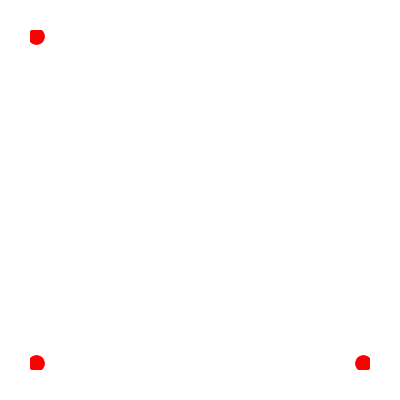

```mathematica
Graphics[{Red,PointSize[0.03],Point[{{0,1},{0,2},{1,1}}]}]
```

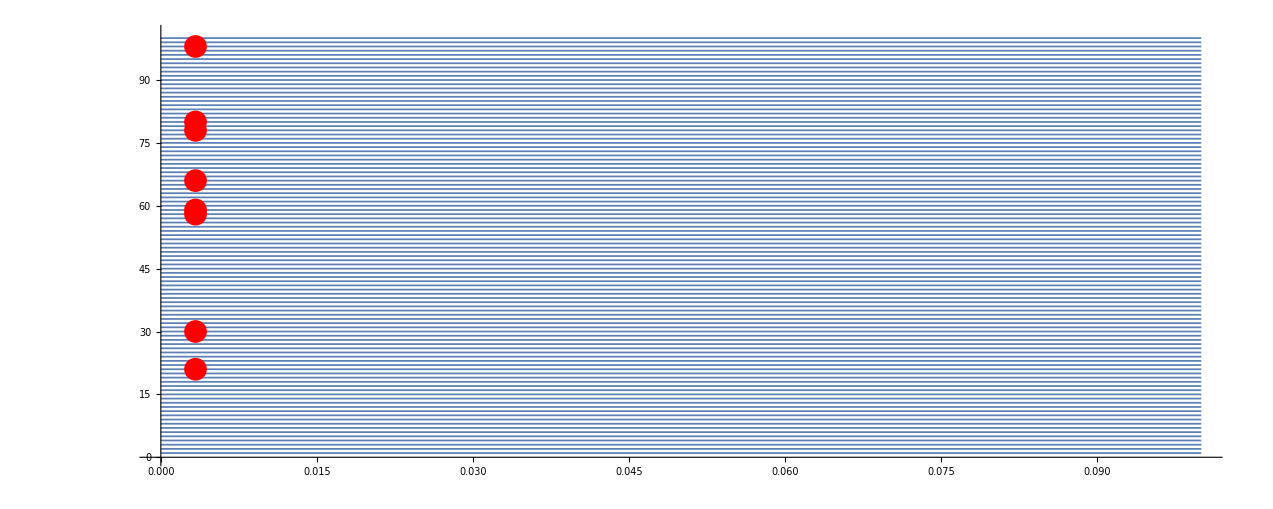

```mathematica
Show[ListPlot[Flatten[Table[{#⟦2⟧,j}&/@Select[pop⟦j⟧,#⟦3⟧==210&],{j,100}],1],PlotStyle->Red],PlotRange->{{0,0.1},{0,101}},AspectRatio->0.4]
```

```mathematica
Select[pop⟦50⟧,#⟦3⟧==200&]
```

{}

```mathematica
pts=Flatten[Table[{#⟦2⟧,j}&/@Select[pop⟦j⟧,#⟦3⟧==200&],{j,100}],1]
```

{{0.0914841,28},{0.0559311,28},{0.0822922,28},{0.0914841,42},{0.0559311,42},{0.0822922,42},{0.0914841,48},{0.0559311,48},{0.0822922,48},{0.0914841,75},{0.0559311,75},{0.0822922,75},{0.0914841,79},{0.0559311,79},{0.0822922,79},{0.0914841,88},{0.0559311,88},{0.0822922,88},{0.0914841,91},{0.0559311,91},{0.0822922,91}}

## Definitions

#### probSurv

```mathematica
probSurv::usage="probSurv[{1,…},r] gives {0,…,1}, the probability of surviving both recombination and coalescence at each time";
probSurv[k_List,r_]:=Reverse[FoldList[#1(1-r)^2(1-1/#2)&,1,Reverse[k]]];
```

#### probCoal

```mathematica
probCoal::usage="probCoal[{1,…},r] sums probSurv*(1/k), to give the net probability of coalescence";
probCoal[k_List,r_]:=Total[Drop[probSurv[k,r],1]/k];
```

#### makeReps

```mathematica
makeReps::usage="makeReps[s,k_max,n_reps,seed] stores n_repsbranching processes, with a Poisson distribution of offspring, stopping at k_max, conditioned on establishment";
makeReps[s_,kmax_,nreps_,seed_]:=makeReps[s,kmax,nreps,seed]=Module[{bp={},np},
rep=0;
While[rep<nreps,
np=NestWhileList[RandomInteger[PoissonDistribution[ # (1+s)]]&,1,(0<#<kmax)&];
If[Last[np]>0,rep+=1;AppendTo[bp,np]]];
bp];
```

#### makeRepsFix

```mathematica
makeRepsFix::usage="makeReps[s,2N,n_reps,seed] stores n_repstrajectories, with a Wright-Fisher model, stopping at k_max, and conditioned on fixation";
makeRepsFix[s_,n_,nreps_,seed_]:=makeRepsFix[s,n,nreps,seed]=Module[{bp={},np},
rep=0;
While[rep<nreps,
np=NestWhileList[RandomInteger[BinomialDistribution[n, (#/n) (1+s)/(1+s (#/n))]]&,1,(0<#<n)&];
If[Last[np]>0,rep+=1;AppendTo[bp,np]]];
bp];
```

#### makeF

```mathematica
makeF::usage="makeF[{1,…},r] gives the identity using the old recursion, which traces forwards in time. makeF[{1,…},2N,r] traces {f_QQ,f_PQ,f_PP} forwards in time.";
makeF[kl_List,r_]:=FoldList[(#1(1-r)^2(1-1/#2)+1/#2)&,1.,Drop[kl,1]];
makeF[kl_List,n_Integer,r_]:=FoldList[iterF[r,n],{0,0,1.},Drop[Drop[kl,1],-1]];
```

#### iterF

```mathematica
iterF::usage="iterF[r,2N][{f_QQ,f_PQ,f_PP},k] iterates IBD forwards in time";
iterF[r_,n_Integer][{fqq_,fpq_,fpp_},k_]:=Module[{p=k/n,q=1-k/n},
{{(1-rp)^2, 2rp(1-rp), (rp)^2}, {(1-rp)rq, ((1-rp)(1-rq)+r^2 pq), rp(1-rq)}, {(rq)^2, 2rq(1-rq), (1-rq)^2}}.{fqq(1-1/(n-k))+1/(n-k),fpq,fpp(1-1/k)+1/k}];
```

#### findT

```mathematica
findT::usage="findT[{1,…},k^*] finds the time at which k_t first exceeds k^*";
findT[s_List,k_]:=First[Pick[Range[Length[s]],(#>k)&/@s]];
```

#### h[ρ]

```mathematica
h::usage="h[ρ] gives the net identity when there are k copies, as h[ρ] (ks).  Found by interpolation in 0<ρ<1.";
h=Interpolation[{{0,1},{0.1,1.102},{0.2,1.253},{0.5,2.170},{0.7,3.52},{1,8.333}}];
```

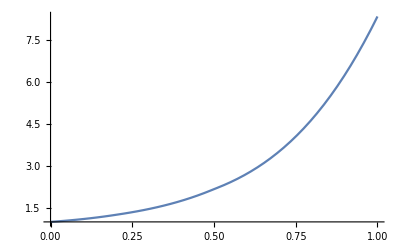

```mathematica
Plot[h[ρ],{ρ,0,1}]
```

#### soln

```mathematica
soln::usage="soln[Ns,ρ,{t_0,t_1}] solves the deterministic recursions for the identities, {fqq,fpq,fpp}. Appropriate for large r.";
soln[Ns_,ρ_,{t0_,t1_}]:=Module[{p},
p[t_]:=1/(1+ⅇ^-t);
NDSolve[{
fqq'[t]==2ρ p[t] (fpq[t]-fqq[t])+(1-fqq[t])/(2Ns (1-p[t])),
fpq'[t]==ρ( (1-p[t])fqq[t]-fpq[t]+p[t]fpp[t]),
fpp'[t]==2ρ(1-p[t]) (fpq[t]-fpp[t])+(1-fpp[t])/(2Ns p[t]),
fqq[t0]==0,fpq[t0]==0,fpp[t0]==0},{fqq,fpq,fpp},{t,t0,t1}]];
```

#### solnApprox

```mathematica
solnApprox::usage="solnApprox[ρ,{t_0,t_1}] solves the deterministic recursions for the scaled identities, {gqq, gpq, gpp}, in the limit of large Ns, when f<<1. Scaled relative to 2Ns. Appropriate for large r.";
solnApprox[ρ_,{t0_,t1_}]:=Module[{p},
p[t_]:=1/(1+ⅇ^-t);
NDSolve[{
gqq'[t]==2ρ p[t] (gpq[t]-gqq[t])+1/(1-p[t]),
gpq'[t]==ρ( (1-p[t])gqq[t]-gpq[t]+p[t]gpp[t]),
gpp'[t]==2ρ(1-p[t]) (gpq[t]-gpp[t])+1/p[t],
gqq[t0]==0,gpq[t0]==0,gpp[t0]==0},{gqq,gpq,gpp},{t,t0,t1}]⟦1⟧];
```

#### solnTr

```mathematica
solnTr::usage="solnTr[ρ,{t_0,t_1}] solves the deterministic recursions for the scaled identities, {g,Δ,δ}}, in the limit of large Ns, when f<<1. Scaled relative to 2Ns. Appropriate for large r.";
solnTr[ρ_,{t0_,t1_}]:=Module[{p},
p[t_]:=1/(1+ⅇ^-t);pq[t_]:=p[t](1-p[t]);
NDSolve[{
g'[t]==2pq[t](2p[t]-1)Δ[t]+(2pq[t])^2 δ[t]+1,
Δ'[t]==-ρ(1+4pq[t]) Δ[t]+pq[t](1+2ρ(2p[t]-1))δ[t]+2,
δ'[t]==2ρ(2p[t]-1)Δ[t]-2ρ(1-2pq[t])δ[t]+(1-2p[t])/pq[t],
g[t0]==0,δ[t0]==0,Δ[t0]==0},{g,δ,Δ},{t,t0,t1}]⟦1⟧];
```

#### coalesce

```mathematica
coalesce::usage="coalesce[{{1},{2,3},{4}},k]  iterates back one generation, assuming population size k. coalesce[{{1},{2,3}},{4},k] adds lineage {4} to the current set of families, assuming that the population is size k";
coalesce[pop_List,k_Integer]:=Fold[coalesce[#1,#2,k]&,{},pop];
coalesce[pop_List,x_List,k_Integer]:=Module[{j=Length[pop]},
If[Random[]<j/k,
MapAt[Join[#,x]&,pop,RandomInteger[{1,j}]],
Append[pop,x]]];
```

#### recombine

```mathematica
recombine::usage="recombine[{{{1},{2},…},{{6},{7},…}},r,p] allows for recombination at rates rq from Q to P, and rp from P to Q.";
recombine[{xq_List,xp_List},r_,p_]:=Module[{xxq,xxp},
xxq=RandomVariate[BernoulliDistribution[r p],Length[xq]];
xxp=RandomVariate[BernoulliDistribution[r(1-p)],Length[xp]];
{Join[Pick[xq,xxq,0],Pick[xp,xxp,1]],
Join[Pick[xq,xxq,1],Pick[xp,xxp,0]]}];
```

#### iterBack

```mathematica
iterBack::usage="iterBack[{{{1},{2},…},{{6},{7},…}},r,2N,k] iterates back one generation, with recombination & then coalescence.";
iterBack[{xq_List,xp_List},r_,n_,k_]:=MapThread[coalesce,{recombine[{xq,xp},r,k/n],{n-k,k}}];
```

#### makeFamilies

```mathematica
makeFamilies::usage="makeFamilies[{1,…,2N},r,2N,J] iterates back the ancestry of J genes, returning the family structure.";
makeFamilies[kl_List,r_,n_,j_Integer]:=Fold[iterBack[#1,r,n,#2]&,{{},List/@Range[j]},Reverse[kl]];
```

#### iterC

```mathematica
iterC::usage="iterC[{{X,{j_1,…},{a_1,…}},…},R,2N,k] iterates back one generation, in a population of 2N with k copies of X=1. The map length is R<1. iterC[{{X,{j_1,…},{a_1,…}},…},R,2N] iterates back one generation, with only background zero. The map length is R<1";
iterC[pop:{{(0|1),_List,_List}..},R_,n_Integer]:=iterC[pop,R,n,0];
iterC[pop:{{(0|1),_List,_List}..},R_,n_Integer,k_Integer]:=
Module[{ng=Length[pop],nr,bp,Y,recInds,repRules,j,npop,npop0,npop1,jj0,jj1},
nr=RandomInteger[BinomialDistribution[ng,R]];
bp=RandomReal[{0,R},nr];recInds=RandomSample[Range[ng],nr];Y=RandomInteger[BernoulliDistribution[k/n],nr];
repRules=MapThread[(#1->recombineC[pop⟦#1⟧,#2,#3])&,{recInds,Y,bp}];
npop=Flatten[ReplacePart[List/@pop,repRules],1];
npop0=Cases[npop,{0,_,_}];npop1=Cases[npop,{1,_,_}];
jj0=RandomInteger[{1,n-k},Length[npop0]];
jj1=RandomInteger[{1,k},Length[npop1]];
condense/@DeleteCases[Join[
coalesceC[npop0⟦Flatten[Position[jj0,#]]⟧]&/@Union[jj0],
coalesceC[npop1⟦Flatten[Position[jj1,#]]⟧]&/@Union[jj1]],{_,_,{{}...}}]];
```

#### makeC

```mathematica
makeC::usage="makeC[n,R,2N] simulates coalescence of n genes in a population of size 2N, on map length R; merges adjacent blocks with the same ancestry, and deletes non-ancestral lineages.  Simulates back until complete coalescence. time and nGenes can be used to track.";
makeC[n_Integer,R_,n2_Integer]:=Module[{i,pop0},
pop0=Table[{0,{},{{i}}},{i,n}];
deleteNA[condense/@#]&/@NestWhileList[(time+=1;nGenes=Length[#1];
iterC[#1,R,n2])&,pop0,Not[coalescedQ[#,n]]&]];
```

#### deleteAllNC

```mathematica
deleteAllNC::usage="deleteAllNC[{{X,{j_1,…},{a_1,…}},…}]  deletes tips and merges blocks that have the same ancestry";
deleteAllNC[pop:{{_,_List,_List}...}]:=deleteAllNC/@pop;
deleteAllNC[{X:(0|1),jl_List,al_List}]:=Module[{jal},
jal=Transpose[Transpose[{Prepend[jl,0],al}]/.{{x_,{_}}:>{x,{}}}];
condense[{X,Drop[jal⟦1⟧,1],jal⟦2⟧}]];
```

#### deleteNC

```mathematica
deleteNC::usage="deleteNC[{{X,{j_1,…},{a_1,…}},…}] deletes lineages that are not coalesced ";
deleteNC[pop:{{_,_List,_List}...}]:=Select[pop,(Max[Length/@#⟦3⟧]>1)&];
```

Note: this definition is used in “HH revisiited” and deletes  tips.

#### deleteNA

```mathematica
deleteNA::usage="deleteNA[{{X,{j_1,…},{a_1,…}},…}] deletes lineages that are not ancestral ";
deleteNA[pop:{{_,_List,_List}...}]:=Select[pop,(Max[Length/@#⟦3⟧]≥1)&];
```

This keeps the tips.

#### condense

```mathematica
condense::usage="condense[{X,{j_1,j_2,…},{a_1,…}}] merges segments that have the same ancestry";
condense[{X_,jl_List,al_List}]:=Module[{jal=Transpose[{Prepend[jl,0],al}]},
jal=Transpose[jal//.{x___,{y_,a_},{_,a_},z___}:>{x,{y,a},z}];
{X,Drop[jal⟦1⟧,1],jal⟦2⟧}];
```

#### randomSet

```mathematica
randomSet::usage="randomSet[n,k] chooses n parents from 1…k, and returns the sizes of sibling families larger than 1";
randomSet[n_Integer,k_Integer]:=Last/@DeleteCases[Sort[Tally[RandomInteger[{1,k},n]]],{_,1}];
```

#### coalesceC

```mathematica
coalesceC::usage="coalesceC[{{X,{j_1,…},{{1,2},…}},{X,{j_1^*,…},{{3,4},…}},…}] produces a single coalesced genome, merging junctions and ancestries. More than two genomes may coalesce.";
coalesceC[g:{{X:(0|1),_List,_List}...}]:=Module[{jt=Union@@g⟦All,2⟧},
{X,jt,(Union@@#)&/@Transpose[MapThread[splitAncestry[#1,#2,jt]&,Transpose[g⟦All,{2,3}⟧]]]}];
```

#### splitAncestry

```mathematica
splitAncestry::usage="splitAncestry[{j_1,j_2,…},{a_1,a_2,…},{j_1^*,j_2^*,…}] extends the list {a_1,a_2,…} by duplicating elements that contain new junctions; j^* lists all junctions. ";
splitAncestry[j1_List,a1_List,j2_List]:=Module[{nn},
nn=1+BinCounts[(1+pos[j1,#])&/@Complement[j2,j1],{1,Length[a1]+1}];
Flatten[MapThread[ConstantArray,{a1,nn}],1]];
```

#### recombineC

```mathematica
recombineC::usage="recombineC[{X,{j_1,…},{{1,2},…},Y,θ] generates two ancestral genomes, breakpoint θ; the partner genome is in state Y, and is assumed non-ancestral";
recombineC[{X:(0|1),jl_List,al_List},Y:(0|1),θ_]:=Module[{pp=pos[jl,θ]},
{{X,Append[jl⟦1;;pp⟧,θ],Append[al⟦1;;(pp+1)⟧,{}]},
{Y,Prepend[jl⟦pp+1;;-1⟧,θ],Prepend[al⟦(pp+1);;-1⟧,{}]}}];
```

```mathematica
TableForm[recombine[{1,{0.02,0.04,0.07},{{1,2},{},{3},{1,5}}},0,#]&/@{0.01,0.03,0.044,0.08},TableDepth->2]
```

{1,{0.01},{{1,2},{}}} | {0,{0.01,0.02,0.04,0.07},{{},{1,2},{},{3},{1,5}}}
{1,{0.02,0.03},{{1,2},{},{}}} | {0,{0.03,0.04,0.07},{{},{},{3},{1,5}}}
{1,{0.02,0.04,0.044},{{1,2},{},{3},{}}} | {0,{0.044,0.07},{{},{3},{1,5}}}
{1,{0.02,0.04,0.07,0.08},{{1,2},{},{3},{1,5},{}}} | {0,{0.08},{{},{1,5}}}

#### pos

```mathematica
pos::usage="pos[{j_1,j_2,…},x] gives the position of the largest j_i smaller than x, or 0 if x<j_1";
pos[jl_List,x_]:=Module[{jl1=Append[jl,∞]},
FirstPosition[jl1,SelectFirst[jl1,(#>x)&]]⟦1⟧-1];
```

#### findBlocks

```mathematica
findBlocks::usage="findBlocks[k,{X,{j_1,…},{a_1,…}}] finds the blocks ancestral to k";
findBlocks[k_,{X_,j_,a_}]:=Module[{al=condense[{X,j,If[MemberQ[#,k],{k},{}]&/@a}]},
If[al⟦3,1⟧=={k},Partition[Prepend[al⟦2⟧,0],2],Partition[al⟦2⟧,2]]];
```

#### findAllBlocks

```mathematica
findAllBlocks::usage="findAllBlocks[k,{{X,{j_1,…},{a_1,…}},...}] finds all blocks ancestral to k, in the form {…,{{j_1,j_2},i},…}, where i is the position in the supplied list of ancestral genomes";
findAllBlocks[k_,pop:{{_,_,_}...}]:=Module[{fb},
fb=MapIndexed[{findBlocks[k,#1],#2}&,pop];
Sort[Flatten[fb/.{{b:{{_,_}...},{i_}}:>({#,i}&/@b)},1]]];
```

#### plotAncestry

```mathematica
plotAncestry::usage="Graphics[plotAncestry[n,{{X,{j_1,…},{a_1,…}},...},cf]] plots the ancestry of genomes 1…n using ColorFunction cf. ";
plotAncestry[n_Integer,pl_List,cf_]:=Module[{na=Length[pl],k},
Flatten[Table[findAllBlocks[k,pl]/.{{x0_,x1_},i_Integer}:>{cf[i/na],Rectangle[{x0,k-1/2},{x1,k+1/2}]},{k,n}],2]];
```

#### coalescedQ

```mathematica
coalescedQ::usage="coalescedQ[{{X,{j_1,…},{a_1,…}},…},n] determines whether all genealogies have coalesced; n is the sample size. Can also be applied to a single genome";
coalescedQ[lin:{(0|1),_List,_List},n_Integer]:=Min[DeleteCases[Length/@lin⟦3⟧,0]]==n;
coalescedQ[pop:{{(0|1),_List,_List}..},n_Integer]:=And@@(coalescedQ[#,n]&/@pop);
```

#### int

```mathematica
int::usage="int[1,{r_1,…},R] gives te interval {0,r_1}";
int[k_Integer,r_List,R_]:=Append[Prepend[r,0],R][[{k,k+1}]];
```

#### branchList

```mathematica
branchList::usage="branchList[{{{X,{..},{..}},..},..}] tallies the branches, returning {{branch,#},…}";
branchList[pop_List]:=Tally[Sort/@DeleteCases[Flatten[pop⟦All,All,3⟧,2],{}]];
```

#### posBlock

```mathematica
posBlock::usage="posBlock[{{{X,{j_1,…},{…}},…},…},{2,13,…},R] returns the generations and blocks covered by this branch, in the form {…,{t,{{r_1,r_2},…},…}.";
posBlock[pop:{{{(0|1),_List,_List}..}..},br_List,R_]:=Module[{posn=Position[pop,br]},
{#⟦1⟧,int[#⟦4⟧,pl2[[#⟦1⟧,#⟦2⟧,2]],R]}&/@posn];
```

#### plotBranch

```mathematica
plotBranch::usage="plotBranch[{2,13},col,{{{X,…},..},..},R] plots blocks on {{0,R},{0,T}}, with the specified colour.";
plotBranch[br_,col_,pop_List,R_]:=Graphics[Join[{col},posBlock[pop,br,R]/.{t_Integer,{r0_,r1_}}:>Rectangle[{r0, (t-1)},{r1, t}]]];
```

#### makeSNP

```mathematica
makeSNP::usage="makeSNP[{{t,{r_0,r_1}}…},μ/r] draws SNP at rate μ/r per map length. The SNP are output as {t,r}, their time of origin and genomic location. The block positions {{t,{r_0,r_1}}…} are generated by posBlock[pop,branch,R]";
makeSNP[posns:{{_Integer,{_,_}}...},μr_]:=Flatten[makeSNP[#,μr]&/@posns,1];
makeSNP[{t_Integer,{r0_,r1_}},μr_]:=Module[{nm},
nm=RandomInteger[PoissonDistribution[μr (r1-r0)]];
{t,#}&/@RandomReal[{r0,r1},nm]];
```